## .00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

### .00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
5.0*Sqrt[3]
```

8.66025

```mathematica
SetOptions[$FrontEndSession,NotebookAutoSave->True]
NotebookSave[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.08@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Eth]?.00.00.00.00.00.00\[Eth]?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00@.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00333333\[ATilde]?.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00

```mathematica
s= 28
```

28

```mathematica
w= .43*s
l = .43*s/Sqrt[3]
h = .867*s/Sqrt[3]
```

12.04

6.9513

14.0158

```mathematica
line[j_,k_] := Table[{i, j, k}, {i, 0-w+.5, w}]
ListPointPlot3D[line[1, 0]]
halfplane  = Flatten[Table[line[j, 0], {j , 0-l*Sqrt[3], l* Sqrt[3], Sqrt[3]}], 1];
Dimensions[%]
```

-Graphics3D-

{336,3}

```mathematica
Join[halfplane, #+{.5, Sqrt[3]/2, 0}&/@halfplane];
plane=%;
Dimensions[%]
```

{672,3}

```mathematica
SortBy[halfplane, First]
```

{{-11.54,-12.04,0},{-11.54,-10.3079,0},{-11.54,-8.5759,0},{-11.54,-6.84385,0},{-11.54,-5.1118,0},{-11.54,-3.37975,0},{-11.54,-1.6477,0},{-11.54,0.0843557,0},{-11.54,1.81641,0},{-11.54,3.54846,0},{-11.54,5.28051,0},{-11.54,7.01256,0},{-11.54,8.74461,0},{-11.54,10.4767,0},{-10.54,-12.04,0},{-10.54,-10.3079,0},{-10.54,-8.5759,0},{-10.54,-6.84385,0},{-10.54,-5.1118,0},{-10.54,-3.37975,0},{-10.54,-1.6477,0},{-10.54,0.0843557,0},{-10.54,1.81641,0},{-10.54,3.54846,0},{-10.54,5.28051,0},{-10.54,7.01256,0},{-10.54,8.74461,0},{-10.54,10.4767,0},{-9.54,-12.04,0},{-9.54,-10.3079,0},{-9.54,-8.5759,0},{-9.54,-6.84385,0},{-9.54,-5.1118,0},{-9.54,-3.37975,0},{-9.54,-1.6477,0},{-9.54,0.0843557,0},{-9.54,1.81641,0},{-9.54,3.54846,0},{-9.54,5.28051,0},{-9.54,7.01256,0},{-9.54,8.74461,0},{-9.54,10.4767,0},{-8.54,-12.04,0},{-8.54,-10.3079,0},{-8.54,-8.5759,0},{-8.54,-6.84385,0},{-8.54,-5.1118,0},{-8.54,-3.37975,0},{-8.54,-1.6477,0},{-8.54,0.0843557,0},{-8.54,1.81641,0},{-8.54,3.54846,0},{-8.54,5.28051,0},{-8.54,7.01256,0},{-8.54,8.74461,0},{-8.54,10.4767,0},{-7.54,-12.04,0},{-7.54,-10.3079,0},{-7.54,-8.5759,0},{-7.54,-6.84385,0},{-7.54,-5.1118,0},{-7.54,-3.37975,0},{-7.54,-1.6477,0},{-7.54,0.0843557,0},{-7.54,1.81641,0},{-7.54,3.54846,0},{-7.54,5.28051,0},{-7.54,7.01256,0},{-7.54,8.74461,0},{-7.54,10.4767,0},{-6.54,-12.04,0},{-6.54,-10.3079,0},{-6.54,-8.5759,0},{-6.54,-6.84385,0},{-6.54,-5.1118,0},{-6.54,-3.37975,0},{-6.54,-1.6477,0},{-6.54,0.0843557,0},{-6.54,1.81641,0},{-6.54,3.54846,0},{-6.54,5.28051,0},{-6.54,7.01256,0},{-6.54,8.74461,0},{-6.54,10.4767,0},{-5.54,-12.04,0},{-5.54,-10.3079,0},{-5.54,-8.5759,0},{-5.54,-6.84385,0},{-5.54,-5.1118,0},{-5.54,-3.37975,0},{-5.54,-1.6477,0},{-5.54,0.0843557,0},{-5.54,1.81641,0},{-5.54,3.54846,0},{-5.54,5.28051,0},{-5.54,7.01256,0},{-5.54,8.74461,0},{-5.54,10.4767,0},{-4.54,-12.04,0},{-4.54,-10.3079,0},{-4.54,-8.5759,0},{-4.54,-6.84385,0},{-4.54,-5.1118,0},{-4.54,-3.37975,0},{-4.54,-1.6477,0},{-4.54,0.0843557,0},{-4.54,1.81641,0},{-4.54,3.54846,0},{-4.54,5.28051,0},{-4.54,7.01256,0},{-4.54,8.74461,0},{-4.54,10.4767,0},{-3.54,-12.04,0},{-3.54,-10.3079,0},{-3.54,-8.5759,0},{-3.54,-6.84385,0},{-3.54,-5.1118,0},{-3.54,-3.37975,0},{-3.54,-1.6477,0},{-3.54,0.0843557,0},{-3.54,1.81641,0},{-3.54,3.54846,0},{-3.54,5.28051,0},{-3.54,7.01256,0},{-3.54,8.74461,0},{-3.54,10.4767,0},{-2.54,-12.04,0},{-2.54,-10.3079,0},{-2.54,-8.5759,0},{-2.54,-6.84385,0},{-2.54,-5.1118,0},{-2.54,-3.37975,0},{-2.54,-1.6477,0},{-2.54,0.0843557,0},{-2.54,1.81641,0},{-2.54,3.54846,0},{-2.54,5.28051,0},{-2.54,7.01256,0},{-2.54,8.74461,0},{-2.54,10.4767,0},{-1.54,-12.04,0},{-1.54,-10.3079,0},{-1.54,-8.5759,0},{-1.54,-6.84385,0},{-1.54,-5.1118,0},{-1.54,-3.37975,0},{-1.54,-1.6477,0},{-1.54,0.0843557,0},{-1.54,1.81641,0},{-1.54,3.54846,0},{-1.54,5.28051,0},{-1.54,7.01256,0},{-1.54,8.74461,0},{-1.54,10.4767,0},{-0.54,-12.04,0},{-0.54,-10.3079,0},{-0.54,-8.5759,0},{-0.54,-6.84385,0},{-0.54,-5.1118,0},{-0.54,-3.37975,0},{-0.54,-1.6477,0},{-0.54,0.0843557,0},{-0.54,1.81641,0},{-0.54,3.54846,0},{-0.54,5.28051,0},{-0.54,7.01256,0},{-0.54,8.74461,0},{-0.54,10.4767,0},{0.46,-12.04,0},{0.46,-10.3079,0},{0.46,-8.5759,0},{0.46,-6.84385,0},{0.46,-5.1118,0},{0.46,-3.37975,0},{0.46,-1.6477,0},{0.46,0.0843557,0},{0.46,1.81641,0},{0.46,3.54846,0},{0.46,5.28051,0},{0.46,7.01256,0},{0.46,8.74461,0},{0.46,10.4767,0},{1.46,-12.04,0},{1.46,-10.3079,0},{1.46,-8.5759,0},{1.46,-6.84385,0},{1.46,-5.1118,0},{1.46,-3.37975,0},{1.46,-1.6477,0},{1.46,0.0843557,0},{1.46,1.81641,0},{1.46,3.54846,0},{1.46,5.28051,0},{1.46,7.01256,0},{1.46,8.74461,0},{1.46,10.4767,0},{2.46,-12.04,0},{2.46,-10.3079,0},{2.46,-8.5759,0},{2.46,-6.84385,0},{2.46,-5.1118,0},{2.46,-3.37975,0},{2.46,-1.6477,0},{2.46,0.0843557,0},{2.46,1.81641,0},{2.46,3.54846,0},{2.46,5.28051,0},{2.46,7.01256,0},{2.46,8.74461,0},{2.46,10.4767,0},{3.46,-12.04,0},{3.46,-10.3079,0},{3.46,-8.5759,0},{3.46,-6.84385,0},{3.46,-5.1118,0},{3.46,-3.37975,0},{3.46,-1.6477,0},{3.46,0.0843557,0},{3.46,1.81641,0},{3.46,3.54846,0},{3.46,5.28051,0},{3.46,7.01256,0},{3.46,8.74461,0},{3.46,10.4767,0},{4.46,-12.04,0},{4.46,-10.3079,0},{4.46,-8.5759,0},{4.46,-6.84385,0},{4.46,-5.1118,0},{4.46,-3.37975,0},{4.46,-1.6477,0},{4.46,0.0843557,0},{4.46,1.81641,0},{4.46,3.54846,0},{4.46,5.28051,0},{4.46,7.01256,0},{4.46,8.74461,0},{4.46,10.4767,0},{5.46,-12.04,0},{5.46,-10.3079,0},{5.46,-8.5759,0},{5.46,-6.84385,0},{5.46,-5.1118,0},{5.46,-3.37975,0},{5.46,-1.6477,0},{5.46,0.0843557,0},{5.46,1.81641,0},{5.46,3.54846,0},{5.46,5.28051,0},{5.46,7.01256,0},{5.46,8.74461,0},{5.46,10.4767,0},{6.46,-12.04,0},{6.46,-10.3079,0},{6.46,-8.5759,0},{6.46,-6.84385,0},{6.46,-5.1118,0},{6.46,-3.37975,0},{6.46,-1.6477,0},{6.46,0.0843557,0},{6.46,1.81641,0},{6.46,3.54846,0},{6.46,5.28051,0},{6.46,7.01256,0},{6.46,8.74461,0},{6.46,10.4767,0},{7.46,-12.04,0},{7.46,-10.3079,0},{7.46,-8.5759,0},{7.46,-6.84385,0},{7.46,-5.1118,0},{7.46,-3.37975,0},{7.46,-1.6477,0},{7.46,0.0843557,0},{7.46,1.81641,0},{7.46,3.54846,0},{7.46,5.28051,0},{7.46,7.01256,0},{7.46,8.74461,0},{7.46,10.4767,0},{8.46,-12.04,0},{8.46,-10.3079,0},{8.46,-8.5759,0},{8.46,-6.84385,0},{8.46,-5.1118,0},{8.46,-3.37975,0},{8.46,-1.6477,0},{8.46,0.0843557,0},{8.46,1.81641,0},{8.46,3.54846,0},{8.46,5.28051,0},{8.46,7.01256,0},{8.46,8.74461,0},{8.46,10.4767,0},{9.46,-12.04,0},{9.46,-10.3079,0},{9.46,-8.5759,0},{9.46,-6.84385,0},{9.46,-5.1118,0},{9.46,-3.37975,0},{9.46,-1.6477,0},{9.46,0.0843557,0},{9.46,1.81641,0},{9.46,3.54846,0},{9.46,5.28051,0},{9.46,7.01256,0},{9.46,8.74461,0},{9.46,10.4767,0},{10.46,-12.04,0},{10.46,-10.3079,0},{10.46,-8.5759,0},{10.46,-6.84385,0},{10.46,-5.1118,0},{10.46,-3.37975,0},{10.46,-1.6477,0},{10.46,0.0843557,0},{10.46,1.81641,0},{10.46,3.54846,0},{10.46,5.28051,0},{10.46,7.01256,0},{10.46,8.74461,0},{10.46,10.4767,0},{11.46,-12.04,0},{11.46,-10.3079,0},{11.46,-8.5759,0},{11.46,-6.84385,0},{11.46,-5.1118,0},{11.46,-3.37975,0},{11.46,-1.6477,0},{11.46,0.0843557,0},{11.46,1.81641,0},{11.46,3.54846,0},{11.46,5.28051,0},{11.46,7.01256,0},{11.46,8.74461,0},{11.46,10.4767,0}}

```mathematica
ListPointPlot3D[halfplane]
```

-Graphics3D-

```mathematica
SortBy[plane, #[[2]]&][[20]][[2]]
```

-12.04

```mathematica
maxx=SortBy[plane, #[[1]]&][[1 ]][[1]]
maxy=SortBy[plane, #[[2]]&][[1 ]][[2]]
```

-11.54

-12.04

```mathematica
planeExtra = {}
firstPlane = {}
If[#[[1]]== maxx, AppendTo[planeExtra, #],If[#[[2]]==maxy,AppendTo[planeExtra, #],AppendTo[firstPlane,#]]]&/@plane
```

{}

{}

{{{-11.54,-12.04,0}},670,{{-10.54,-10.3079,0},{-9.54,-10.3079,0},{-8.54,-10.3079,0},{-7.54,-10.3079,0},{-6.54,-10.3079,0},{-5.54,-10.3079,0},{-4.54,-10.3079,0},{-3.54,-10.3079,0},619,{4.96,11.3427,0},{5.96,11.3427,0},{6.96,11.3427,0},{7.96,11.3427,0},{8.96,11.3427,0},{9.96,11.3427,0},{10.96,11.3427,0},{11.96,11.3427,0}}}
 |  |  |  |

```mathematica
ListPointPlot3D[%, AxesLabel->{x,y,z}, PlotRange->All, PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
(*firstPlane = Join[firstPlane, line[-3Sqrt[3],0], line[4Sqrt[3],0]]*);
```

```mathematica
SortBy[firstPlane, #[[2]]&][[25]][[2]]
```

-10.3079

```mathematica
ListPointPlot3D[%]
```

-Graphics3D-

```mathematica
ListPointPlot3D[plane]
```

-Graphics3D-

```mathematica
ListPointPlot3D[firstPlane*1/s, AspectRatio->1, AxesLabel ->  {x, y, z} ]
```

-Graphics3D-

```mathematica
Length[firstPlane]
```

635

```mathematica
Area[BoundingRegion[#[[1;;2]]&/@firstPlane*1/s, "MinRectangle"]]/Length[firstPlane]
```

0.00104026

```mathematica
frontbackplane = Join[firstPlane*1/s,  (# - {0, 0, (h)Sqrt[3]})&/@firstPlane*1/s];
ListPointPlot3D[frontbackplane]
bases = %;
```

-Graphics3D-

```mathematica
10-3 √3*1.0
```

4.80385

```mathematica
4.803847577293368
```

4.80385

```mathematica
SortBy[frontbackplane, First][[1]]
SortBy[frontbackplane, First][[-1]]
```

{-0.394286,-0.399071,-0.867}

{0.427143,0.405096,0}

```mathematica
Sort[{9.75,5.196152422706632,0.}]
```

{0.,5.19615,9.75}

```mathematica
line[j_,k_] := Table[{i, j, k}, {i, 0-w+.5, w}]
```

```mathematica
Flatten[Table[line[-(l)*Sqrt[3], k], {k ,0-(h)* Sqrt[3] ,0 , Sqrt[3]}], 1];
left = Join[%, #-{.5, 0, Sqrt[3]/2}&/@%];
maxz1 = SortBy[left, Last][[1]][[3]]
maxx1 = SortBy[left, First][[1]][[1]]
planeExtra = {}
leftplane = {}
If[#[[3]]== maxz1, AppendTo[planeExtra, #],If[#[[1]]==maxx1,AppendTo[planeExtra, #],AppendTo[leftplane,#]]]&/@left;
ListPointPlot3D[%]
leftplanepic = ListPointPlot3D[leftplane*1/s, AxesLabel-> {x,y,z}]
```

-25.142

-12.04

{}

{}

-Graphics3D-

-Graphics3D-

```mathematica
Extraplanepic = ListPointPlot3D[planeExtra*1/s, AxesLabel-> {x,y,z}]
```

-Graphics3D-

```mathematica
SortBy[frontbackplane, First];
```

```mathematica
2.401923788646684-2.151923788646684
```

0.25

```mathematica
ListPointPlot3D[{(#+{-1/(2s),-Sqrt[3]/(2*s),0})&/@frontbackplane, leftplane*1/s}, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
arch = Join[leftplane*1/s, (#+{-1/(2s),-Sqrt[3]/(2*s),0})&/@frontbackplane];
```

```mathematica
Show[ListPointPlot3D[arch], PlotRange-> All, AxesLabel-> {x,y,z}]

arcbox = %
```

-Graphics3D-

-Graphics3D-

```mathematica
SortBy[firstPlane, #[[2]]&][[1]][[2]]- SortBy[firstPlane, #[[2]]&][[-1]][[2]]

tunnelpoints = Join[arch,  (# + {0,-(SortBy[firstPlane, #[[2]]&][[1]][[2]]- SortBy[firstPlane, #[[2]]&][[-1]][[2]]), 0})&/@leftplane*1/s];
(*Flatten[Table[line[l*Sqrt[3]+ Sqrt[3]/2, k], {k ,0-h*Sqrt[3]-Sqrt[3]/2,0, Sqrt[3]}], 1];
Join[%, #+{-.5, 0, Sqrt[3]/2}&/@%];
rightplane = %;
rightplanepic = ListPointPlot3D[%]*)
```

-22.5167

```mathematica
tunnel = ListPointPlot3D[tunnelpoints, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
(*Show[arcbox, rightplanepic]
tunnel = %*)
```

```mathematica
(* line[j_,k_] := Table[{i, j, k}, {i, -10, 10}]

halfplane  = Flatten[Table[line[j, 0], {j , -3 Sqrt[3], 3 Sqrt[3], Sqrt[3]}], 1];
Join[halfplane, #+{.5, Sqrt[3]/2, 0}&/@halfplane];

Flatten[Table[line[3Sqrt[3]+ Sqrt[3]/2, k], {k ,-3Sqrt[3]-Sqrt[3]/2,0, Sqrt[3]}], 1];
Join[%, #+{-.5, 0, Sqrt[3]/2}&/@%];
rightplane = %;
rightplanepic = ListPointPlot3D[%]*)

line1[i_,k_] := Table[{i, j, k}, {j, -l*Sqrt[3]+Sqrt[3],l*Sqrt[3] + Sqrt[3], Sqrt[3]}]
```

```mathematica
SortBy[frontbackplane, #[[1]]&][[-1]]
```

{0.427143,0.405096,0}

```mathematica
w*1.0
```

12.04

```mathematica
34-w
```

21.96

```mathematica
topplaneExtra= {}
topplane1 = {}
Flatten[Table[line1[w-.5, k], {k, 0-(h)*Sqrt[3], 0, Sqrt[3]}],1];
```

{}

{}

```mathematica
Join[%,#-{0,Sqrt[3]/2, Sqrt[3]/2} & /@%];
```

```mathematica
If[#[[3]]== SortBy[%, #[[3]]][[Length[%]]][[3]] , AppendTo[topplaneExtra, #], If[#[[2]] == SortBy[%, #[[2]]][[Length[%]]][[2]],AppendTo[topplaneExtra, #] ,AppendTo[topplane1,#]]]&/@%;
```

```mathematica
ListPointPlot3D[%, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
topplane;
```

```mathematica
2.348076211353316-2.151923788646684
```

0.196152

```mathematica
topplane2=  (#-{0,0,0})&/@topplane1*1/s;
topplane = (#+{SortBy[tunnelpoints, #[[1]]&][[-1]][[1]]- SortBy[topplane2, #[[1]]&][[-1]][[1]],SortBy[tunnelpoints, #[[2]]&][[-1]][[2]]- SortBy[topplane2, #[[2]]&][[-1]][[2]],SortBy[tunnelpoints, #[[3]]&][[1]][[3]]- SortBy[topplane2, #[[3]]&][[1]][[3]]})&/@topplane2;
topplanepic = ListPointPlot3D[topplane, AxesLabel->{i, j, k}, PlotStyle->Red]
```

-Graphics3D-

```mathematica
SortBy[tunnelpoints, #[[3]]&][[1]][[3]]- SortBy[topplane, #[[3]]&][[1]][[3]]
```

0.

```mathematica
Show[tunnel,topplanepic, AxesLabel ->  {i,j,k}, PlotRange-> All]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[1], BoundingRegion[tunnelpoints]}, Axes->True, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

```mathematica
Show[%339, %338]
```

Show::gcomb: Could not combine the graphics objects in Show[Null,Null].

Show[Null,Null]

```mathematica
almostBox = Join[tunnelpoints, topplane];
```

```mathematica
SortBy[firstPlane, #[[1]]&][[1]][[1]]- SortBy[firstPlane, #[[1]]&][[-1]][[1]]
box = Join[almostBox,  (# + {(SortBy[firstPlane, #[[1]]&][[1]][[1]]- SortBy[firstPlane, #[[1]]&][[-1]][[1]])*1/s,0, 0})&/@topplane];
```

-23.

```mathematica
SortBy[tunnelpoints, First][[Length[tunnelpoints]]]
SortBy[tunnelpoints, First][[25]][[1]]-SortBy[tunnelpoints, First][[Length[tunnelpoints]]][[1]]
```

{0.409286,0.374166,0}

-0.821429

```mathematica
w/2-SortBy[tunnelpoints, First][[Length[tunnelpoints]]][[1]]
```

5.61071

```mathematica
ListPointPlot3D[box, PlotRange->All, AxesLabel->{x,y,z}]
```

-Graphics3D-

```mathematica
.5/1.1
```

0.454545

```mathematica
Sqrt[3]/4*1.0
```

0.433013

```mathematica
(*bottomplane= {}
bottomplaneExtra = {}*)
```

```mathematica
(*Flatten[Table[line1[0-w-.5, k], {k, 0-(h+1)*Sqrt[3], 0, Sqrt[3]}],1];*)
```

```mathematica
(*Join[%,#-{0,Sqrt[3]/2, Sqrt[3]/2} & /@%];*)
```

```mathematica
(*If[#[[3]]== (-9Sqrt[3])/2 , AppendTo[bottomplaneExtra, #],AppendTo[bottomplane,#]]&/@%*)
```

```mathematica
(*bottomplane*)
```

```mathematica
(*bottomplanepic = ListPointPlot3D[bottomplane, AxesLabel->{i, j, k}, PlotStyle->Red]*)
```

```mathematica
(* *)
```

```mathematica
(*Show[%511, %370]*)
```

```mathematica
(*Show[tunnel, bottomplanepic,topplanepic, AxesLabel ->  {i,j,k}, PlotRangePadding -> 1]
bow = %;*)
```

```mathematica
box = N[box];

box[[2]]
```

{-0.376429,-0.43,-0.867}

```mathematica
Length[box]
```

3418

```mathematica
box = N[Round[#, 10^-5]&/@box];
```

```mathematica
boxSquished = Round[#, 10^-3]&/@boxSquished;
```

```mathematica
box1 = DeleteDuplicates[box];
Length[%]
```

3286

```mathematica
boxSquished = {#[[1]], (#[[2]])/1.075, #[[3]]}&/@ box;
```

```mathematica
boxSquished= N[boxSquished];
```

```mathematica
ListPointPlot3D[box, PlotStyle->PointSize[Large]]
```

-Graphics3D-

```mathematica
Graphics3D[{Opacity[1], BoundingRegion[box]}, Axes->True, AxesLabel->{"x", "y", "z"}]
```

-Graphics3D-

```mathematica
Show[%742, %743]
```

Show::gcomb: Could not combine the graphics objects in Show[Null,{{0.410909,-0.390635,-0.827635},{0.410909,-0.311906,-0.827635},{0.410909,-0.233176,-0.827635},{0.410909,-0.154446,-0.827635},{0.410909,-0.0757169,-0.827635},{0.410909,0.0030127,-0.827635},«40»,{0.410909,0.0817423,-0.512717},{0.410909,0.160472,-0.512717},{0.410909,0.239201,-0.512717},{0.410909,0.317931,-0.512717},«192»}].

Show[Null,{{0.410909,-0.390635,-0.827635},{0.410909,-0.311906,-0.827635},{0.410909,-0.233176,-0.827635},{0.410909,-0.154446,-0.827635},{0.410909,-0.0757169,-0.827635},{0.410909,0.0030127,-0.827635},{0.410909,0.0817423,-0.827635},{0.410909,0.160472,-0.827635},{0.410909,0.239201,-0.827635},{0.410909,0.317931,-0.827635},{0.410909,-0.390635,-0.748906},{0.410909,-0.311906,-0.748906},{0.410909,-0.233176,-0.748906},{0.410909,-0.154446,-0.748906},{0.410909,-0.0757169,-0.748906},{0.410909,0.0030127,-0.748906},{0.410909,0.0817423,-0.748906},{0.410909,0.160472,-0.748906},{0.410909,0.239201,-0.748906},{0.410909,0.317931,-0.748906},{0.410909,-0.390635,-0.670176},{0.410909,-0.311906,-0.670176},{0.410909,-0.233176,-0.670176},{0.410909,-0.154446,-0.670176},{0.410909,-0.0757169,-0.670176},{0.410909,0.0030127,-0.670176},{0.410909,0.0817423,-0.670176},{0.410909,0.160472,-0.670176},{0.410909,0.239201,-0.670176},{0.410909,0.317931,-0.670176},{0.410909,-0.390635,-0.591446},{0.410909,-0.311906,-0.591446},{0.410909,-0.233176,-0.591446},{0.410909,-0.154446,-0.591446},{0.410909,-0.0757169,-0.591446},{0.410909,0.0030127,-0.591446},{0.410909,0.0817423,-0.591446},{0.410909,0.160472,-0.591446},{0.410909,0.239201,-0.591446},{0.410909,0.317931,-0.591446},{0.410909,-0.390635,-0.512717},{0.410909,-0.311906,-0.512717},{0.410909,-0.233176,-0.512717},{0.410909,-0.154446,-0.512717},{0.410909,-0.0757169,-0.512717},{0.410909,0.0030127,-0.512717},{0.410909,0.0817423,-0.512717},{0.410909,0.160472,-0.512717},{0.410909,0.239201,-0.512717},{0.410909,0.317931,-0.512717},{0.410909,-0.390635,-0.433987},{0.410909,-0.311906,-0.433987},{0.410909,-0.233176,-0.433987},{0.410909,-0.154446,-0.433987},{0.410909,-0.0757169,-0.433987},{0.410909,0.0030127,-0.433987},{0.410909,0.0817423,-0.433987},{0.410909,0.160472,-0.433987},{0.410909,0.239201,-0.433987},{0.410909,0.317931,-0.433987},{0.410909,-0.390635,-0.355258},{0.410909,-0.311906,-0.355258},{0.410909,-0.233176,-0.355258},{0.410909,-0.154446,-0.355258},{0.410909,-0.0757169,-0.355258},{0.410909,0.0030127,-0.355258},{0.410909,0.0817423,-0.355258},{0.410909,0.160472,-0.355258},{0.410909,0.239201,-0.355258},{0.410909,0.317931,-0.355258},{0.410909,-0.390635,-0.276528},{0.410909,-0.311906,-0.276528},{0.410909,-0.233176,-0.276528},{0.410909,-0.154446,-0.276528},{0.410909,-0.0757169,-0.276528},{0.410909,0.0030127,-0.276528},{0.410909,0.0817423,-0.276528},{0.410909,0.160472,-0.276528},{0.410909,0.239201,-0.276528},{0.410909,0.317931,-0.276528},{0.410909,-0.390635,-0.197799},{0.410909,-0.311906,-0.197799},{0.410909,-0.233176,-0.197799},{0.410909,-0.154446,-0.197799},{0.410909,-0.0757169,-0.197799},{0.410909,0.0030127,-0.197799},{0.410909,0.0817423,-0.197799},{0.410909,0.160472,-0.197799},{0.410909,0.239201,-0.197799},{0.410909,0.317931,-0.197799},{0.410909,-0.390635,-0.119069},{0.410909,-0.311906,-0.119069},{0.410909,-0.233176,-0.119069},{0.410909,-0.154446,-0.119069},{0.410909,-0.0757169,-0.119069},{0.410909,0.0030127,-0.119069},{0.410909,0.0817423,-0.119069},{0.410909,0.160472,-0.119069},{0.410909,0.239201,-0.119069},{0.410909,0.317931,-0.119069},{0.410909,-0.390635,-0.0403394},{0.410909,-0.311906,-0.0403394},{0.410909,-0.233176,-0.0403394},{0.410909,-0.154446,-0.0403394},{0.410909,-0.0757169,-0.0403394},{0.410909,0.0030127,-0.0403394},{0.410909,0.0817423,-0.0403394},{0.410909,0.160472,-0.0403394},{0.410909,0.239201,-0.0403394},{0.410909,0.317931,-0.0403394},{0.410909,-0.43,-0.867},{0.410909,-0.35127,-0.867},{0.410909,-0.272541,-0.867},{0.410909,-0.193811,-0.867},{0.410909,-0.115082,-0.867},{0.410909,-0.0363521,-0.867},{0.410909,0.0423775,-0.867},{0.410909,0.121107,-0.867},{0.410909,0.199837,-0.867},{0.410909,0.278566,-0.867},{0.410909,0.357296,-0.867},{0.410909,-0.43,-0.78827},{0.410909,-0.35127,-0.78827},{0.410909,-0.272541,-0.78827},{0.410909,-0.193811,-0.78827},{0.410909,-0.115082,-0.78827},{0.410909,-0.0363521,-0.78827},{0.410909,0.0423775,-0.78827},{0.410909,0.121107,-0.78827},{0.410909,0.199837,-0.78827},{0.410909,0.278566,-0.78827},{0.410909,0.357296,-0.78827},{0.410909,-0.43,-0.709541},{0.410909,-0.35127,-0.709541},{0.410909,-0.272541,-0.709541},{0.410909,-0.193811,-0.709541},{0.410909,-0.115082,-0.709541},{0.410909,-0.0363521,-0.709541},{0.410909,0.0423775,-0.709541},{0.410909,0.121107,-0.709541},{0.410909,0.199837,-0.709541},{0.410909,0.278566,-0.709541},{0.410909,0.357296,-0.709541},{0.410909,-0.43,-0.630811},{0.410909,-0.35127,-0.630811},{0.410909,-0.272541,-0.630811},{0.410909,-0.193811,-0.630811},{0.410909,-0.115082,-0.630811},{0.410909,-0.0363521,-0.630811},{0.410909,0.0423775,-0.630811},{0.410909,0.121107,-0.630811},{0.410909,0.199837,-0.630811},{0.410909,0.278566,-0.630811},{0.410909,0.357296,-0.630811},{0.410909,-0.43,-0.552082},{0.410909,-0.35127,-0.552082},{0.410909,-0.272541,-0.552082},{0.410909,-0.193811,-0.552082},{0.410909,-0.115082,-0.552082},{0.410909,-0.0363521,-0.552082},{0.410909,0.0423775,-0.552082},{0.410909,0.121107,-0.552082},{0.410909,0.199837,-0.552082},{0.410909,0.278566,-0.552082},{0.410909,0.357296,-0.552082},{0.410909,-0.43,-0.473352},{0.410909,-0.35127,-0.473352},{0.410909,-0.272541,-0.473352},{0.410909,-0.193811,-0.473352},{0.410909,-0.115082,-0.473352},{0.410909,-0.0363521,-0.473352},{0.410909,0.0423775,-0.473352},{0.410909,0.121107,-0.473352},{0.410909,0.199837,-0.473352},{0.410909,0.278566,-0.473352},{0.410909,0.357296,-0.473352},{0.410909,-0.43,-0.394623},{0.410909,-0.35127,-0.394623},{0.410909,-0.272541,-0.394623},{0.410909,-0.193811,-0.394623},{0.410909,-0.115082,-0.394623},{0.410909,-0.0363521,-0.394623},{0.410909,0.0423775,-0.394623},{0.410909,0.121107,-0.394623},{0.410909,0.199837,-0.394623},{0.410909,0.278566,-0.394623},{0.410909,0.357296,-0.394623},{0.410909,-0.43,-0.315893},{0.410909,-0.35127,-0.315893},{0.410909,-0.272541,-0.315893},{0.410909,-0.193811,-0.315893},{0.410909,-0.115082,-0.315893},{0.410909,-0.0363521,-0.315893},{0.410909,0.0423775,-0.315893},{0.410909,0.121107,-0.315893},{0.410909,0.199837,-0.315893},{0.410909,0.278566,-0.315893},{0.410909,0.357296,-0.315893},{0.410909,-0.43,-0.237163},{0.410909,-0.35127,-0.237163},{0.410909,-0.272541,-0.237163},{0.410909,-0.193811,-0.237163},{0.410909,-0.115082,-0.237163},{0.410909,-0.0363521,-0.237163},{0.410909,0.0423775,-0.237163},{0.410909,0.121107,-0.237163},{0.410909,0.199837,-0.237163},{0.410909,0.278566,-0.237163},{0.410909,0.357296,-0.237163},{0.410909,-0.43,-0.158434},{0.410909,-0.35127,-0.158434},{0.410909,-0.272541,-0.158434},{0.410909,-0.193811,-0.158434},{0.410909,-0.115082,-0.158434},{0.410909,-0.0363521,-0.158434},{0.410909,0.0423775,-0.158434},{0.410909,0.121107,-0.158434},{0.410909,0.199837,-0.158434},{0.410909,0.278566,-0.158434},{0.410909,0.357296,-0.158434},{0.410909,-0.43,-0.0797042},{0.410909,-0.35127,-0.0797042},{0.410909,-0.272541,-0.0797042},{0.410909,-0.193811,-0.0797042},{0.410909,-0.115082,-0.0797042},{0.410909,-0.0363521,-0.0797042},{0.410909,0.0423775,-0.0797042},{0.410909,0.121107,-0.0797042},{0.410909,0.199837,-0.0797042},{0.410909,0.278566,-0.0797042},{0.410909,0.357296,-0.0797042},{0.410909,-0.43,-0.000974596},{0.410909,-0.35127,-0.000974596},{0.410909,-0.272541,-0.000974596},{0.410909,-0.193811,-0.000974596},{0.410909,-0.115082,-0.000974596},{0.410909,-0.0363521,-0.000974596},{0.410909,0.0423775,-0.000974596},{0.410909,0.121107,-0.000974596},{0.410909,0.199837,-0.000974596},{0.410909,0.278566,-0.000974596},{0.410909,0.357296,-0.000974596}}]

```mathematica
c=RegionCentroid[Point[box1]]
```

{-0.00142776,-0.0279158,-0.424311}

```mathematica
boxCentered = N[#-c &/@ box1];
```

```mathematica
BoundingRegion[boxCentered]
```

Cuboid[{-0.410712,-0.402084,-0.442689},{0.410718,0.402086,0.424311}]

```mathematica
collectDups[l_]:=Block[{i},i[n_]:=(i[n]=n;Unevaluated@Sequence[]);i/@l]
```

```mathematica
collectDups[box]
```

{{-0.41214,-0.43,-0.867},{-0.37643,-0.43,-0.867},{-0.34071,-0.43,-0.867},{-0.305,-0.43,-0.867},{-0.26929,-0.43,-0.867},{-0.23357,-0.43,-0.867},{-0.19786,-0.43,-0.867},{-0.16214,-0.43,-0.867},{-0.12643,-0.43,-0.867},{-0.09071,-0.43,-0.867},{-0.055,-0.43,-0.867},{-0.01929,-0.43,-0.867},{0.01643,-0.43,-0.867},{0.05214,-0.43,-0.867},{0.08786,-0.43,-0.867},{0.12357,-0.43,-0.867},{0.15929,-0.43,-0.867},{0.195,-0.43,-0.867},{0.23071,-0.43,-0.867},{0.26643,-0.43,-0.867},{0.30214,-0.43,-0.867},{0.33786,-0.43,-0.867},{0.37357,-0.43,-0.867},{0.40929,-0.43,-0.867},{-0.41214,0.37417,-0.867},{-0.37643,0.37417,-0.867},{-0.34071,0.37417,-0.867},{-0.305,0.37417,-0.867},{-0.26929,0.37417,-0.867},{-0.23357,0.37417,-0.867},{-0.19786,0.37417,-0.867},{-0.16214,0.37417,-0.867},{-0.12643,0.37417,-0.867},{-0.09071,0.37417,-0.867},{-0.055,0.37417,-0.867},{-0.01929,0.37417,-0.867},{0.01643,0.37417,-0.867},{0.05214,0.37417,-0.867},{0.08786,0.37417,-0.867},{0.12357,0.37417,-0.867},{0.15929,0.37417,-0.867},{0.195,0.37417,-0.867},{0.23071,0.37417,-0.867},{0.26643,0.37417,-0.867},{0.30214,0.37417,-0.867},{0.33786,0.37417,-0.867},{0.37357,0.37417,-0.867},{0.40929,0.37417,-0.867},{0.40929,-0.43,-0.867},{0.40929,-0.36814,-0.867},{0.40929,-0.30628,-0.867},{0.40929,-0.24442,-0.867},{0.40929,-0.18256,-0.867},{0.40929,-0.12071,-0.867},{0.40929,-0.05885,-0.867},{0.40929,0.00301,-0.867},{0.40929,0.06487,-0.867},{0.40929,0.12673,-0.867},{0.40929,0.18859,-0.867},{0.40929,0.25045,-0.867},{0.40929,0.31231,-0.867},{0.40929,0.37417,-0.867},{0.40929,-0.43,-0.80514},{0.40929,0.37417,-0.80514},{0.40929,-0.43,-0.74328},{0.40929,0.37417,-0.74328},{0.40929,-0.43,-0.68142},{0.40929,0.37417,-0.68142},{0.40929,-0.43,-0.61956},{0.40929,0.37417,-0.61956},{0.40929,-0.43,-0.55771},{0.40929,0.37417,-0.55771},{0.40929,-0.43,-0.49585},{0.40929,0.37417,-0.49585},{0.40929,-0.43,-0.43399},{0.40929,0.37417,-0.43399},{0.40929,-0.43,-0.37213},{0.40929,0.37417,-0.37213},{0.40929,-0.43,-0.31027},{0.40929,0.37417,-0.31027},{0.40929,-0.43,-0.24841},{0.40929,0.37417,-0.24841},{0.40929,-0.43,-0.18655},{0.40929,0.37417,-0.18655},{0.40929,-0.43,-0.12469},{0.40929,0.37417,-0.12469},{0.40929,-0.43,-0.06283},{0.40929,0.37417,-0.06283},{0.40929,-0.43,-0.00097},{0.40929,0.37417,-0.00097},{-0.41214,-0.43,-0.867},{-0.41214,-0.36814,-0.867},{-0.41214,-0.30628,-0.867},{-0.41214,-0.24442,-0.867},{-0.41214,-0.18256,-0.867},{-0.41214,-0.12071,-0.867},{-0.41214,-0.05885,-0.867},{-0.41214,0.00301,-0.867},{-0.41214,0.06487,-0.867},{-0.41214,0.12673,-0.867},{-0.41214,0.18859,-0.867},{-0.41214,0.25045,-0.867},{-0.41214,0.31231,-0.867},{-0.41214,0.37417,-0.867},{-0.41214,-0.43,-0.80514},{-0.41214,0.37417,-0.80514},{-0.41214,-0.43,-0.74328},{-0.41214,0.37417,-0.74328},{-0.41214,-0.43,-0.68142},{-0.41214,0.37417,-0.68142},{-0.41214,-0.43,-0.61956},{-0.41214,0.37417,-0.61956},{-0.41214,-0.43,-0.55771},{-0.41214,0.37417,-0.55771},{-0.41214,-0.43,-0.49585},{-0.41214,0.37417,-0.49585},{-0.41214,-0.43,-0.43399},{-0.41214,0.37417,-0.43399},{-0.41214,-0.43,-0.37213},{-0.41214,0.37417,-0.37213},{-0.41214,-0.43,-0.31027},{-0.41214,0.37417,-0.31027},{-0.41214,-0.43,-0.24841},{-0.41214,0.37417,-0.24841},{-0.41214,-0.43,-0.18655},{-0.41214,0.37417,-0.18655},{-0.41214,-0.43,-0.12469},{-0.41214,0.37417,-0.12469},{-0.41214,-0.43,-0.06283},{-0.41214,0.37417,-0.06283},{-0.41214,-0.43,-0.00097},{-0.41214,0.37417,-0.00097}}

```mathematica
ListPointPlot3D[{DeleteDuplicates[box]}]
```

-Graphics3D-

```mathematica
boxCentered1 = DeleteDuplicates[boxCentered];
```

```mathematica
Length[boxCentered]
Length[boxCentered1]
```

3286

3286

```mathematica
Show[%1140, %1139]
```

Show::gcomb: Could not combine the graphics objects in Show[%1140,%1139].

Show[%1140,%1139]

```mathematica
SortBy[box, #[[3]]&][[295]][[3]]- SortBy[firstPlane, #[[3]]&][[-1]][[3]]
```

-0.867

```mathematica
DumpSave[".mx", "Global`"]
```

{Global`}

```mathematica
boxCentered[[2]]
```

{-0.375002,-0.402084,-0.442689}

```mathematica
Directory[]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj

```mathematica
Export["C:\\Users\\Lara\\Documents\\Physics\\Witten\\Electrophoreses\\Electrophoresis\\ComputationalPhysicsFinalProj\\smallDenseBoxS28.csv", boxCentered]
```

C:\Users\Lara\Documents\Physics\Witten\Electrophoreses\Electrophoresis\ComputationalPhysicsFinalProj\smallDenseBoxS28.csv

```mathematica
boxCentered = #-RegionCentroid[Point[box]] &/@ box;
```

$Aborted

```mathematica
SortBy[boxCentered, #[[3]]&][[1]]
SortBy[boxCentered, #[[3]]&][[987]]
```

{-0.392861,-0.371154,-0.452174}

Part::partw: Part 987 of {{-0.392861,-0.371154,-0.452174},{-0.392861,-0.371154,-0.452174},{-0.392861,-0.371154,-0.452174},{-0.392861,-0.247434,-0.452174},{-0.392861,-0.247434,-0.452174},{-0.392861,-0.123714,-0.452174},«40»,{-0.214281,-0.309294,-0.452174},{-0.214281,-0.185574,-0.452174},{-0.214281,-0.0618643,-0.452174},{-0.214281,0.0618557,-0.452174},«792»} does not exist.

{{-0.392861,-0.371154,-0.452174},{-0.392861,-0.371154,-0.452174},{-0.392861,-0.371154,-0.452174},{-0.392861,-0.247434,-0.452174},{-0.392861,-0.247434,-0.452174},{-0.392861,-0.123714,-0.452174},{-0.392861,-0.123714,-0.452174},{-0.392861,-4.29124×10^-6,-0.452174},{-0.392861,-4.29124×10^-6,-0.452174},{-0.392861,0.123716,-0.452174},{-0.392861,0.123716,-0.452174},{-0.392861,0.247436,-0.452174},{-0.392861,0.247436,-0.452174},{-0.392861,0.371156,-0.452174},{-0.392861,0.371156,-0.452174},{-0.392861,0.371156,-0.452174},{-0.357141,-0.309294,-0.452174},{-0.357141,-0.185574,-0.452174},{-0.357141,-0.0618643,-0.452174},{-0.357141,0.0618557,-0.452174},{-0.357141,0.185576,-0.452174},{-0.357141,0.309296,-0.452174},{-0.321431,-0.371154,-0.452174},{-0.321431,-0.371154,-0.452174},{-0.321431,-0.247434,-0.452174},{-0.321431,-0.123714,-0.452174},{-0.321431,-4.29124×10^-6,-0.452174},{-0.321431,0.123716,-0.452174},{-0.321431,0.247436,-0.452174},{-0.321431,0.371156,-0.452174},{-0.321431,0.371156,-0.452174},{-0.285711,-0.309294,-0.452174},{-0.285711,-0.185574,-0.452174},{-0.285711,-0.0618643,-0.452174},{-0.285711,0.0618557,-0.452174},{-0.285711,0.185576,-0.452174},{-0.285711,0.309296,-0.452174},{-0.250001,-0.371154,-0.452174},{-0.250001,-0.371154,-0.452174},{-0.250001,-0.247434,-0.452174},{-0.250001,-0.123714,-0.452174},{-0.250001,-4.29124×10^-6,-0.452174},{-0.250001,0.123716,-0.452174},{-0.250001,0.247436,-0.452174},{-0.250001,0.371156,-0.452174},{-0.250001,0.371156,-0.452174},{-0.214281,-0.309294,-0.452174},{-0.214281,-0.185574,-0.452174},{-0.214281,-0.0618643,-0.452174},{-0.214281,0.0618557,-0.452174},{-0.214281,0.185576,-0.452174},{-0.214281,0.309296,-0.452174},{-0.178571,-0.371154,-0.452174},{-0.178571,-0.371154,-0.452174},{-0.178571,-0.247434,-0.452174},{-0.178571,-0.123714,-0.452174},{-0.178571,-4.29124×10^-6,-0.452174},{-0.178571,0.123716,-0.452174},{-0.178571,0.247436,-0.452174},{-0.178571,0.371156,-0.452174},{-0.178571,0.371156,-0.452174},{-0.142861,-0.309294,-0.452174},{-0.142861,-0.185574,-0.452174},{-0.142861,-0.0618643,-0.452174},{-0.142861,0.0618557,-0.452174},{-0.142861,0.185576,-0.452174},{-0.142861,0.309296,-0.452174},{-0.107141,-0.371154,-0.452174},{-0.107141,-0.371154,-0.452174},{-0.107141,-0.247434,-0.452174},{-0.107141,-0.123714,-0.452174},{-0.107141,-4.29124×10^-6,-0.452174},{-0.107141,0.123716,-0.452174},{-0.107141,0.247436,-0.452174},{-0.107141,0.371156,-0.452174},{-0.107141,0.371156,-0.452174},{-0.071431,-0.309294,-0.452174},{-0.071431,-0.185574,-0.452174},{-0.071431,-0.0618643,-0.452174},{-0.071431,0.0618557,-0.452174},{-0.071431,0.185576,-0.452174},{-0.071431,0.309296,-0.452174},{-0.035711,-0.371154,-0.452174},{-0.035711,-0.371154,-0.452174},{-0.035711,-0.247434,-0.452174},{-0.035711,-0.123714,-0.452174},{-0.035711,-4.29124×10^-6,-0.452174},{-0.035711,0.123716,-0.452174},{-0.035711,0.247436,-0.452174},{-0.035711,0.371156,-0.452174},{-0.035711,0.371156,-0.452174},{-1.03093×10^-6,-0.309294,-0.452174},{-1.03093×10^-6,-0.185574,-0.452174},{-1.03093×10^-6,-0.0618643,-0.452174},{-1.03093×10^-6,0.0618557,-0.452174},{-1.03093×10^-6,0.185576,-0.452174},{-1.03093×10^-6,0.309296,-0.452174},{0.035719,-0.371154,-0.452174},{0.035719,-0.371154,-0.452174},{0.035719,-0.247434,-0.452174},{0.035719,-0.123714,-0.452174},{0.035719,-4.29124×10^-6,-0.452174},{0.035719,0.123716,-0.452174},{0.035719,0.247436,-0.452174},{0.035719,0.371156,-0.452174},{0.035719,0.371156,-0.452174},{0.071429,-0.309294,-0.452174},{0.071429,-0.185574,-0.452174},{0.071429,-0.0618643,-0.452174},{0.071429,0.0618557,-0.452174},{0.071429,0.185576,-0.452174},{0.071429,0.309296,-0.452174},{0.107139,-0.371154,-0.452174},{0.107139,-0.371154,-0.452174},{0.107139,-0.247434,-0.452174},{0.107139,-0.123714,-0.452174},{0.107139,-4.29124×10^-6,-0.452174},{0.107139,0.123716,-0.452174},{0.107139,0.247436,-0.452174},{0.107139,0.371156,-0.452174},{0.107139,0.371156,-0.452174},{0.142859,-0.309294,-0.452174},{0.142859,-0.185574,-0.452174},{0.142859,-0.0618643,-0.452174},{0.142859,0.0618557,-0.452174},{0.142859,0.185576,-0.452174},{0.142859,0.309296,-0.452174},{0.178569,-0.371154,-0.452174},{0.178569,-0.371154,-0.452174},{0.178569,-0.247434,-0.452174},{0.178569,-0.123714,-0.452174},{0.178569,-4.29124×10^-6,-0.452174},{0.178569,0.123716,-0.452174},{0.178569,0.247436,-0.452174},{0.178569,0.371156,-0.452174},{0.178569,0.371156,-0.452174},{0.214289,-0.309294,-0.452174},{0.214289,-0.185574,-0.452174},{0.214289,-0.0618643,-0.452174},{0.214289,0.0618557,-0.452174},{0.214289,0.185576,-0.452174},{0.214289,0.309296,-0.452174},{0.249999,-0.371154,-0.452174},{0.249999,-0.371154,-0.452174},{0.249999,-0.247434,-0.452174},{0.249999,-0.123714,-0.452174},{0.249999,-4.29124×10^-6,-0.452174},{0.249999,0.123716,-0.452174},{0.249999,0.247436,-0.452174},{0.249999,0.371156,-0.452174},{0.249999,0.371156,-0.452174},{0.285719,-0.309294,-0.452174},{0.285719,-0.185574,-0.452174},{0.285719,-0.0618643,-0.452174},{0.285719,0.0618557,-0.452174},{0.285719,0.185576,-0.452174},{0.285719,0.309296,-0.452174},{0.321429,-0.371154,-0.452174},{0.321429,-0.371154,-0.452174},{0.321429,-0.247434,-0.452174},{0.321429,-0.123714,-0.452174},{0.321429,-4.29124×10^-6,-0.452174},{0.321429,0.123716,-0.452174},{0.321429,0.247436,-0.452174},{0.321429,0.371156,-0.452174},{0.321429,0.371156,-0.452174},{0.357139,-0.309294,-0.452174},{0.357139,-0.185574,-0.452174},{0.357139,-0.0618643,-0.452174},{0.357139,0.0618557,-0.452174},{0.357139,0.185576,-0.452174},{0.357139,0.309296,-0.452174},{0.392859,-0.371154,-0.452174},{0.392859,-0.371154,-0.452174},{0.392859,-0.371154,-0.452174},{0.392859,-0.247434,-0.452174},{0.392859,-0.247434,-0.452174},{0.392859,-0.123714,-0.452174},{0.392859,-0.123714,-0.452174},{0.392859,-4.29124×10^-6,-0.452174},{0.392859,-4.29124×10^-6,-0.452174},{0.392859,0.123716,-0.452174},{0.392859,0.123716,-0.452174},{0.392859,0.247436,-0.452174},{0.392859,0.247436,-0.452174},{0.392859,0.371156,-0.452174},{0.392859,0.371156,-0.452174},{0.392859,0.371156,-0.452174},{-0.392861,-0.309294,-0.390314},{-0.392861,-0.185574,-0.390314},{-0.392861,-0.0618643,-0.390314},{-0.392861,0.0618557,-0.390314},{-0.392861,0.185576,-0.390314},{-0.392861,0.309296,-0.390314},{-0.357141,-0.371154,-0.390314},{-0.357141,0.371156,-0.390314},{-0.285711,-0.371154,-0.390314},{-0.285711,0.371156,-0.390314},{-0.214281,-0.371154,-0.390314},{-0.214281,0.371156,-0.390314},{-0.142861,-0.371154,-0.390314},{-0.142861,0.371156,-0.390314},{-0.071431,-0.371154,-0.390314},{-0.071431,0.371156,-0.390314},{-1.03093×10^-6,-0.371154,-0.390314},{-1.03093×10^-6,0.371156,-0.390314},{0.071429,-0.371154,-0.390314},{0.071429,0.371156,-0.390314},{0.142859,-0.371154,-0.390314},{0.142859,0.371156,-0.390314},{0.214289,-0.371154,-0.390314},{0.214289,0.371156,-0.390314},{0.285719,-0.371154,-0.390314},{0.285719,0.371156,-0.390314},{0.357139,-0.371154,-0.390314},{0.357139,0.371156,-0.390314},{0.392859,-0.309294,-0.390314},{0.392859,-0.185574,-0.390314},{0.392859,-0.0618643,-0.390314},{0.392859,0.0618557,-0.390314},{0.392859,0.185576,-0.390314},{0.392859,0.309296,-0.390314},{-0.392861,-0.371154,-0.328454},{-0.392861,-0.371154,-0.328454},{-0.392861,-0.247434,-0.328454},{-0.392861,-0.123714,-0.328454},{-0.392861,-4.29124×10^-6,-0.328454},{-0.392861,0.123716,-0.328454},{-0.392861,0.247436,-0.328454},{-0.392861,0.371156,-0.328454},{-0.392861,0.371156,-0.328454},{-0.321431,-0.371154,-0.328454},{-0.321431,0.371156,-0.328454},{-0.250001,-0.371154,-0.328454},{-0.250001,0.371156,-0.328454},{-0.178571,-0.371154,-0.328454},{-0.178571,0.371156,-0.328454},{-0.107141,-0.371154,-0.328454},{-0.107141,0.371156,-0.328454},{-0.035711,-0.371154,-0.328454},{-0.035711,0.371156,-0.328454},{0.035719,-0.371154,-0.328454},{0.035719,0.371156,-0.328454},{0.107139,-0.371154,-0.328454},{0.107139,0.371156,-0.328454},{0.178569,-0.371154,-0.328454},{0.178569,0.371156,-0.328454},{0.249999,-0.371154,-0.328454},{0.249999,0.371156,-0.328454},{0.321429,-0.371154,-0.328454},{0.321429,0.371156,-0.328454},{0.392859,-0.371154,-0.328454},{0.392859,-0.371154,-0.328454},{0.392859,-0.247434,-0.328454},{0.392859,-0.123714,-0.328454},{0.392859,-4.29124×10^-6,-0.328454},{0.392859,0.123716,-0.328454},{0.392859,0.247436,-0.328454},{0.392859,0.371156,-0.328454},{0.392859,0.371156,-0.328454},{-0.392861,-0.309294,-0.266594},{-0.392861,-0.185574,-0.266594},{-0.392861,-0.0618643,-0.266594},{-0.392861,0.0618557,-0.266594},{-0.392861,0.185576,-0.266594},{-0.392861,0.309296,-0.266594},{-0.357141,-0.371154,-0.266594},{-0.357141,0.371156,-0.266594},{-0.285711,-0.371154,-0.266594},{-0.285711,0.371156,-0.266594},{-0.214281,-0.371154,-0.266594},{-0.214281,0.371156,-0.266594},{-0.142861,-0.371154,-0.266594},{-0.142861,0.371156,-0.266594},{-0.071431,-0.371154,-0.266594},{-0.071431,0.371156,-0.266594},{-1.03093×10^-6,-0.371154,-0.266594},{-1.03093×10^-6,0.371156,-0.266594},{0.071429,-0.371154,-0.266594},{0.071429,0.371156,-0.266594},{0.142859,-0.371154,-0.266594},{0.142859,0.371156,-0.266594},{0.214289,-0.371154,-0.266594},{0.214289,0.371156,-0.266594},{0.285719,-0.371154,-0.266594},{0.285719,0.371156,-0.266594},{0.357139,-0.371154,-0.266594},{0.357139,0.371156,-0.266594},{0.392859,-0.309294,-0.266594},{0.392859,-0.185574,-0.266594},{0.392859,-0.0618643,-0.266594},{0.392859,0.0618557,-0.266594},{0.392859,0.185576,-0.266594},{0.392859,0.309296,-0.266594},{-0.392861,-0.371154,-0.204734},{-0.392861,-0.371154,-0.204734},{-0.392861,-0.247434,-0.204734},{-0.392861,-0.123714,-0.204734},{-0.392861,-4.29124×10^-6,-0.204734},{-0.392861,0.123716,-0.204734},{-0.392861,0.247436,-0.204734},{-0.392861,0.371156,-0.204734},{-0.392861,0.371156,-0.204734},{-0.321431,-0.371154,-0.204734},{-0.321431,0.371156,-0.204734},{-0.250001,-0.371154,-0.204734},{-0.250001,0.371156,-0.204734},{-0.178571,-0.371154,-0.204734},{-0.178571,0.371156,-0.204734},{-0.107141,-0.371154,-0.204734},{-0.107141,0.371156,-0.204734},{-0.035711,-0.371154,-0.204734},{-0.035711,0.371156,-0.204734},{0.035719,-0.371154,-0.204734},{0.035719,0.371156,-0.204734},{0.107139,-0.371154,-0.204734},{0.107139,0.371156,-0.204734},{0.178569,-0.371154,-0.204734},{0.178569,0.371156,-0.204734},{0.249999,-0.371154,-0.204734},{0.249999,0.371156,-0.204734},{0.321429,-0.371154,-0.204734},{0.321429,0.371156,-0.204734},{0.392859,-0.371154,-0.204734},{0.392859,-0.371154,-0.204734},{0.392859,-0.247434,-0.204734},{0.392859,-0.123714,-0.204734},{0.392859,-4.29124×10^-6,-0.204734},{0.392859,0.123716,-0.204734},{0.392859,0.247436,-0.204734},{0.392859,0.371156,-0.204734},{0.392859,0.371156,-0.204734},{-0.392861,-0.309294,-0.142884},{-0.392861,-0.185574,-0.142884},{-0.392861,-0.0618643,-0.142884},{-0.392861,0.0618557,-0.142884},{-0.392861,0.185576,-0.142884},{-0.392861,0.309296,-0.142884},{-0.357141,-0.371154,-0.142884},{-0.357141,0.371156,-0.142884},{-0.285711,-0.371154,-0.142884},{-0.285711,0.371156,-0.142884},{-0.214281,-0.371154,-0.142884},{-0.214281,0.371156,-0.142884},{-0.142861,-0.371154,-0.142884},{-0.142861,0.371156,-0.142884},{-0.071431,-0.371154,-0.142884},{-0.071431,0.371156,-0.142884},{-1.03093×10^-6,-0.371154,-0.142884},{-1.03093×10^-6,0.371156,-0.142884},{0.071429,-0.371154,-0.142884},{0.071429,0.371156,-0.142884},{0.142859,-0.371154,-0.142884},{0.142859,0.371156,-0.142884},{0.214289,-0.371154,-0.142884},{0.214289,0.371156,-0.142884},{0.285719,-0.371154,-0.142884},{0.285719,0.371156,-0.142884},{0.357139,-0.371154,-0.142884},{0.357139,0.371156,-0.142884},{0.392859,-0.309294,-0.142884},{0.392859,-0.185574,-0.142884},{0.392859,-0.0618643,-0.142884},{0.392859,0.0618557,-0.142884},{0.392859,0.185576,-0.142884},{0.392859,0.309296,-0.142884},{-0.392861,-0.371154,-0.0810237},{-0.392861,-0.371154,-0.0810237},{-0.392861,-0.247434,-0.0810237},{-0.392861,-0.123714,-0.0810237},{-0.392861,-4.29124×10^-6,-0.0810237},{-0.392861,0.123716,-0.0810237},{-0.392861,0.247436,-0.0810237},{-0.392861,0.371156,-0.0810237},{-0.392861,0.371156,-0.0810237},{-0.321431,-0.371154,-0.0810237},{-0.321431,0.371156,-0.0810237},{-0.250001,-0.371154,-0.0810237},{-0.250001,0.371156,-0.0810237},{-0.178571,-0.371154,-0.0810237},{-0.178571,0.371156,-0.0810237},{-0.107141,-0.371154,-0.0810237},{-0.107141,0.371156,-0.0810237},{-0.035711,-0.371154,-0.0810237},{-0.035711,0.371156,-0.0810237},{0.035719,-0.371154,-0.0810237},{0.035719,0.371156,-0.0810237},{0.107139,-0.371154,-0.0810237},{0.107139,0.371156,-0.0810237},{0.178569,-0.371154,-0.0810237},{0.178569,0.371156,-0.0810237},{0.249999,-0.371154,-0.0810237},{0.249999,0.371156,-0.0810237},{0.321429,-0.371154,-0.0810237},{0.321429,0.371156,-0.0810237},{0.392859,-0.371154,-0.0810237},{0.392859,-0.371154,-0.0810237},{0.392859,-0.247434,-0.0810237},{0.392859,-0.123714,-0.0810237},{0.392859,-4.29124×10^-6,-0.0810237},{0.392859,0.123716,-0.0810237},{0.392859,0.247436,-0.0810237},{0.392859,0.371156,-0.0810237},{0.392859,0.371156,-0.0810237},{-0.392861,-0.309294,-0.0191637},{-0.392861,-0.185574,-0.0191637},{-0.392861,-0.0618643,-0.0191637},{-0.392861,0.0618557,-0.0191637},{-0.392861,0.185576,-0.0191637},{-0.392861,0.309296,-0.0191637},{-0.357141,-0.371154,-0.0191637},{-0.357141,0.371156,-0.0191637},{-0.285711,-0.371154,-0.0191637},{-0.285711,0.371156,-0.0191637},{-0.214281,-0.371154,-0.0191637},{-0.214281,0.371156,-0.0191637},{-0.142861,-0.371154,-0.0191637},{-0.142861,0.371156,-0.0191637},{-0.071431,-0.371154,-0.0191637},{-0.071431,0.371156,-0.0191637},{-1.03093×10^-6,-0.371154,-0.0191637},{-1.03093×10^-6,0.371156,-0.0191637},{0.071429,-0.371154,-0.0191637},{0.071429,0.371156,-0.0191637},{0.142859,-0.371154,-0.0191637},{0.142859,0.371156,-0.0191637},{0.214289,-0.371154,-0.0191637},{0.214289,0.371156,-0.0191637},{0.285719,-0.371154,-0.0191637},{0.285719,0.371156,-0.0191637},{0.357139,-0.371154,-0.0191637},{0.357139,0.371156,-0.0191637},{0.392859,-0.309294,-0.0191637},{0.392859,-0.185574,-0.0191637},{0.392859,-0.0618643,-0.0191637},{0.392859,0.0618557,-0.0191637},{0.392859,0.185576,-0.0191637},{0.392859,0.309296,-0.0191637},{-0.392861,-0.371154,0.0426963},{-0.392861,-0.371154,0.0426963},{-0.392861,-0.247434,0.0426963},{-0.392861,-0.123714,0.0426963},{-0.392861,-4.29124×10^-6,0.0426963},{-0.392861,0.123716,0.0426963},{-0.392861,0.247436,0.0426963},{-0.392861,0.371156,0.0426963},{-0.392861,0.371156,0.0426963},{-0.321431,-0.371154,0.0426963},{-0.321431,0.371156,0.0426963},{-0.250001,-0.371154,0.0426963},{-0.250001,0.371156,0.0426963},{-0.178571,-0.371154,0.0426963},{-0.178571,0.371156,0.0426963},{-0.107141,-0.371154,0.0426963},{-0.107141,0.371156,0.0426963},{-0.035711,-0.371154,0.0426963},{-0.035711,0.371156,0.0426963},{0.035719,-0.371154,0.0426963},{0.035719,0.371156,0.0426963},{0.107139,-0.371154,0.0426963},{0.107139,0.371156,0.0426963},{0.178569,-0.371154,0.0426963},{0.178569,0.371156,0.0426963},{0.249999,-0.371154,0.0426963},{0.249999,0.371156,0.0426963},{0.321429,-0.371154,0.0426963},{0.321429,0.371156,0.0426963},{0.392859,-0.371154,0.0426963},{0.392859,-0.371154,0.0426963},{0.392859,-0.247434,0.0426963},{0.392859,-0.123714,0.0426963},{0.392859,-4.29124×10^-6,0.0426963},{0.392859,0.123716,0.0426963},{0.392859,0.247436,0.0426963},{0.392859,0.371156,0.0426963},{0.392859,0.371156,0.0426963},{-0.392861,-0.309294,0.104556},{-0.392861,-0.185574,0.104556},{-0.392861,-0.0618643,0.104556},{-0.392861,0.0618557,0.104556},{-0.392861,0.185576,0.104556},{-0.392861,0.309296,0.104556},{-0.357141,-0.371154,0.104556},{-0.357141,0.371156,0.104556},{-0.285711,-0.371154,0.104556},{-0.285711,0.371156,0.104556},{-0.214281,-0.371154,0.104556},{-0.214281,0.371156,0.104556},{-0.142861,-0.371154,0.104556},{-0.142861,0.371156,0.104556},{-0.071431,-0.371154,0.104556},{-0.071431,0.371156,0.104556},{-1.03093×10^-6,-0.371154,0.104556},{-1.03093×10^-6,0.371156,0.104556},{0.071429,-0.371154,0.104556},{0.071429,0.371156,0.104556},{0.142859,-0.371154,0.104556},{0.142859,0.371156,0.104556},{0.214289,-0.371154,0.104556},{0.214289,0.371156,0.104556},{0.285719,-0.371154,0.104556},{0.285719,0.371156,0.104556},{0.357139,-0.371154,0.104556},{0.357139,0.371156,0.104556},{0.392859,-0.309294,0.104556},{0.392859,-0.185574,0.104556},{0.392859,-0.0618643,0.104556},{0.392859,0.0618557,0.104556},{0.392859,0.185576,0.104556},{0.392859,0.309296,0.104556},{-0.392861,-0.371154,0.166416},{-0.392861,-0.371154,0.166416},{-0.392861,-0.247434,0.166416},{-0.392861,-0.123714,0.166416},{-0.392861,-4.29124×10^-6,0.166416},{-0.392861,0.123716,0.166416},{-0.392861,0.247436,0.166416},{-0.392861,0.371156,0.166416},{-0.392861,0.371156,0.166416},{-0.321431,-0.371154,0.166416},{-0.321431,0.371156,0.166416},{-0.250001,-0.371154,0.166416},{-0.250001,0.371156,0.166416},{-0.178571,-0.371154,0.166416},{-0.178571,0.371156,0.166416},{-0.107141,-0.371154,0.166416},{-0.107141,0.371156,0.166416},{-0.035711,-0.371154,0.166416},{-0.035711,0.371156,0.166416},{0.035719,-0.371154,0.166416},{0.035719,0.371156,0.166416},{0.107139,-0.371154,0.166416},{0.107139,0.371156,0.166416},{0.178569,-0.371154,0.166416},{0.178569,0.371156,0.166416},{0.249999,-0.371154,0.166416},{0.249999,0.371156,0.166416},{0.321429,-0.371154,0.166416},{0.321429,0.371156,0.166416},{0.392859,-0.371154,0.166416},{0.392859,-0.371154,0.166416},{0.392859,-0.247434,0.166416},{0.392859,-0.123714,0.166416},{0.392859,-4.29124×10^-6,0.166416},{0.392859,0.123716,0.166416},{0.392859,0.247436,0.166416},{0.392859,0.371156,0.166416},{0.392859,0.371156,0.166416},{-0.392861,-0.309294,0.228276},{-0.392861,-0.185574,0.228276},{-0.392861,-0.0618643,0.228276},{-0.392861,0.0618557,0.228276},{-0.392861,0.185576,0.228276},{-0.392861,0.309296,0.228276},{-0.357141,-0.371154,0.228276},{-0.357141,0.371156,0.228276},{-0.285711,-0.371154,0.228276},{-0.285711,0.371156,0.228276},{-0.214281,-0.371154,0.228276},{-0.214281,0.371156,0.228276},{-0.142861,-0.371154,0.228276},{-0.142861,0.371156,0.228276},{-0.071431,-0.371154,0.228276},{-0.071431,0.371156,0.228276},{-1.03093×10^-6,-0.371154,0.228276},{-1.03093×10^-6,0.371156,0.228276},{0.071429,-0.371154,0.228276},{0.071429,0.371156,0.228276},{0.142859,-0.371154,0.228276},{0.142859,0.371156,0.228276},{0.214289,-0.371154,0.228276},{0.214289,0.371156,0.228276},{0.285719,-0.371154,0.228276},{0.285719,0.371156,0.228276},{0.357139,-0.371154,0.228276},{0.357139,0.371156,0.228276},{0.392859,-0.309294,0.228276},{0.392859,-0.185574,0.228276},{0.392859,-0.0618643,0.228276},{0.392859,0.0618557,0.228276},{0.392859,0.185576,0.228276},{0.392859,0.309296,0.228276},{-0.392861,-0.371154,0.290136},{-0.392861,-0.371154,0.290136},{-0.392861,-0.247434,0.290136},{-0.392861,-0.123714,0.290136},{-0.392861,-4.29124×10^-6,0.290136},{-0.392861,0.123716,0.290136},{-0.392861,0.247436,0.290136},{-0.392861,0.371156,0.290136},{-0.392861,0.371156,0.290136},{-0.321431,-0.371154,0.290136},{-0.321431,0.371156,0.290136},{-0.250001,-0.371154,0.290136},{-0.250001,0.371156,0.290136},{-0.178571,-0.371154,0.290136},{-0.178571,0.371156,0.290136},{-0.107141,-0.371154,0.290136},{-0.107141,0.371156,0.290136},{-0.035711,-0.371154,0.290136},{-0.035711,0.371156,0.290136},{0.035719,-0.371154,0.290136},{0.035719,0.371156,0.290136},{0.107139,-0.371154,0.290136},{0.107139,0.371156,0.290136},{0.178569,-0.371154,0.290136},{0.178569,0.371156,0.290136},{0.249999,-0.371154,0.290136},{0.249999,0.371156,0.290136},{0.321429,-0.371154,0.290136},{0.321429,0.371156,0.290136},{0.392859,-0.371154,0.290136},{0.392859,-0.371154,0.290136},{0.392859,-0.247434,0.290136},{0.392859,-0.123714,0.290136},{0.392859,-4.29124×10^-6,0.290136},{0.392859,0.123716,0.290136},{0.392859,0.247436,0.290136},{0.392859,0.371156,0.290136},{0.392859,0.371156,0.290136},{-0.392861,-0.309294,0.351996},{-0.392861,-0.185574,0.351996},{-0.392861,-0.0618643,0.351996},{-0.392861,0.0618557,0.351996},{-0.392861,0.185576,0.351996},{-0.392861,0.309296,0.351996},{-0.357141,-0.371154,0.351996},{-0.357141,0.371156,0.351996},{-0.285711,-0.371154,0.351996},{-0.285711,0.371156,0.351996},{-0.214281,-0.371154,0.351996},{-0.214281,0.371156,0.351996},{-0.142861,-0.371154,0.351996},{-0.142861,0.371156,0.351996},{-0.071431,-0.371154,0.351996},{-0.071431,0.371156,0.351996},{-1.03093×10^-6,-0.371154,0.351996},{-1.03093×10^-6,0.371156,0.351996},{0.071429,-0.371154,0.351996},{0.071429,0.371156,0.351996},{0.142859,-0.371154,0.351996},{0.142859,0.371156,0.351996},{0.214289,-0.371154,0.351996},{0.214289,0.371156,0.351996},{0.285719,-0.371154,0.351996},{0.285719,0.371156,0.351996},{0.357139,-0.371154,0.351996},{0.357139,0.371156,0.351996},{0.392859,-0.309294,0.351996},{0.392859,-0.185574,0.351996},{0.392859,-0.0618643,0.351996},{0.392859,0.0618557,0.351996},{0.392859,0.185576,0.351996},{0.392859,0.309296,0.351996},{-0.392861,-0.371154,0.413856},{-0.392861,-0.371154,0.413856},{-0.392861,-0.247434,0.413856},{-0.392861,-0.123714,0.413856},{-0.392861,-4.29124×10^-6,0.413856},{-0.392861,0.123716,0.413856},{-0.392861,0.247436,0.413856},{-0.392861,0.371156,0.413856},{-0.392861,0.371156,0.413856},{-0.321431,-0.371154,0.413856},{-0.321431,0.371156,0.413856},{-0.250001,-0.371154,0.413856},{-0.250001,0.371156,0.413856},{-0.178571,-0.371154,0.413856},{-0.178571,0.371156,0.413856},{-0.107141,-0.371154,0.413856},{-0.107141,0.371156,0.413856},{-0.035711,-0.371154,0.413856},{-0.035711,0.371156,0.413856},{0.035719,-0.371154,0.413856},{0.035719,0.371156,0.413856},{0.107139,-0.371154,0.413856},{0.107139,0.371156,0.413856},{0.178569,-0.371154,0.413856},{0.178569,0.371156,0.413856},{0.249999,-0.371154,0.413856},{0.249999,0.371156,0.413856},{0.321429,-0.371154,0.413856},{0.321429,0.371156,0.413856},{0.392859,-0.371154,0.413856},{0.392859,-0.371154,0.413856},{0.392859,-0.247434,0.413856},{0.392859,-0.123714,0.413856},{0.392859,-4.29124×10^-6,0.413856},{0.392859,0.123716,0.413856},{0.392859,0.247436,0.413856},{0.392859,0.371156,0.413856},{0.392859,0.371156,0.413856},{-0.392861,-0.371154,0.414826},{-0.392861,-0.247434,0.414826},{-0.392861,-0.123714,0.414826},{-0.392861,-4.29124×10^-6,0.414826},{-0.392861,0.123716,0.414826},{-0.392861,0.247436,0.414826},{-0.392861,0.371156,0.414826},{-0.357141,-0.309294,0.414826},{-0.357141,-0.185574,0.414826},{-0.357141,-0.0618643,0.414826},{-0.357141,0.0618557,0.414826},{-0.357141,0.185576,0.414826},{-0.357141,0.309296,0.414826},{-0.321431,-0.371154,0.414826},{-0.321431,-0.247434,0.414826},{-0.321431,-0.123714,0.414826},{-0.321431,-4.29124×10^-6,0.414826},{-0.321431,0.123716,0.414826},{-0.321431,0.247436,0.414826},{-0.321431,0.371156,0.414826},{-0.285711,-0.309294,0.414826},{-0.285711,-0.185574,0.414826},{-0.285711,-0.0618643,0.414826},{-0.285711,0.0618557,0.414826},{-0.285711,0.185576,0.414826},{-0.285711,0.309296,0.414826},{-0.250001,-0.371154,0.414826},{-0.250001,-0.247434,0.414826},{-0.250001,-0.123714,0.414826},{-0.250001,-4.29124×10^-6,0.414826},{-0.250001,0.123716,0.414826},{-0.250001,0.247436,0.414826},{-0.250001,0.371156,0.414826},{-0.214281,-0.309294,0.414826},{-0.214281,-0.185574,0.414826},{-0.214281,-0.0618643,0.414826},{-0.214281,0.0618557,0.414826},{-0.214281,0.185576,0.414826},{-0.214281,0.309296,0.414826},{-0.178571,-0.371154,0.414826},{-0.178571,-0.247434,0.414826},{-0.178571,-0.123714,0.414826},{-0.178571,-4.29124×10^-6,0.414826},{-0.178571,0.123716,0.414826},{-0.178571,0.247436,0.414826},{-0.178571,0.371156,0.414826},{-0.142861,-0.309294,0.414826},{-0.142861,-0.185574,0.414826},{-0.142861,-0.0618643,0.414826},{-0.142861,0.0618557,0.414826},{-0.142861,0.185576,0.414826},{-0.142861,0.309296,0.414826},{-0.107141,-0.371154,0.414826},{-0.107141,-0.247434,0.414826},{-0.107141,-0.123714,0.414826},{-0.107141,-4.29124×10^-6,0.414826},{-0.107141,0.123716,0.414826},{-0.107141,0.247436,0.414826},{-0.107141,0.371156,0.414826},{-0.071431,-0.309294,0.414826},{-0.071431,-0.185574,0.414826},{-0.071431,-0.0618643,0.414826},{-0.071431,0.0618557,0.414826},{-0.071431,0.185576,0.414826},{-0.071431,0.309296,0.414826},{-0.035711,-0.371154,0.414826},{-0.035711,-0.247434,0.414826},{-0.035711,-0.123714,0.414826},{-0.035711,-4.29124×10^-6,0.414826},{-0.035711,0.123716,0.414826},{-0.035711,0.247436,0.414826},{-0.035711,0.371156,0.414826},{-1.03093×10^-6,-0.309294,0.414826},{-1.03093×10^-6,-0.185574,0.414826},{-1.03093×10^-6,-0.0618643,0.414826},{-1.03093×10^-6,0.0618557,0.414826},{-1.03093×10^-6,0.185576,0.414826},{-1.03093×10^-6,0.309296,0.414826},{0.035719,-0.371154,0.414826},{0.035719,-0.247434,0.414826},{0.035719,-0.123714,0.414826},{0.035719,-4.29124×10^-6,0.414826},{0.035719,0.123716,0.414826},{0.035719,0.247436,0.414826},{0.035719,0.371156,0.414826},{0.071429,-0.309294,0.414826},{0.071429,-0.185574,0.414826},{0.071429,-0.0618643,0.414826},{0.071429,0.0618557,0.414826},{0.071429,0.185576,0.414826},{0.071429,0.309296,0.414826},{0.107139,-0.371154,0.414826},{0.107139,-0.247434,0.414826},{0.107139,-0.123714,0.414826},{0.107139,-4.29124×10^-6,0.414826},{0.107139,0.123716,0.414826},{0.107139,0.247436,0.414826},{0.107139,0.371156,0.414826},{0.142859,-0.309294,0.414826},{0.142859,-0.185574,0.414826},{0.142859,-0.0618643,0.414826},{0.142859,0.0618557,0.414826},{0.142859,0.185576,0.414826},{0.142859,0.309296,0.414826},{0.178569,-0.371154,0.414826},{0.178569,-0.247434,0.414826},{0.178569,-0.123714,0.414826},{0.178569,-4.29124×10^-6,0.414826},{0.178569,0.123716,0.414826},{0.178569,0.247436,0.414826},{0.178569,0.371156,0.414826},{0.214289,-0.309294,0.414826},{0.214289,-0.185574,0.414826},{0.214289,-0.0618643,0.414826},{0.214289,0.0618557,0.414826},{0.214289,0.185576,0.414826},{0.214289,0.309296,0.414826},{0.249999,-0.371154,0.414826},{0.249999,-0.247434,0.414826},{0.249999,-0.123714,0.414826},{0.249999,-4.29124×10^-6,0.414826},{0.249999,0.123716,0.414826},{0.249999,0.247436,0.414826},{0.249999,0.371156,0.414826},{0.285719,-0.309294,0.414826},{0.285719,-0.185574,0.414826},{0.285719,-0.0618643,0.414826},{0.285719,0.0618557,0.414826},{0.285719,0.185576,0.414826},{0.285719,0.309296,0.414826},{0.321429,-0.371154,0.414826},{0.321429,-0.247434,0.414826},{0.321429,-0.123714,0.414826},{0.321429,-4.29124×10^-6,0.414826},{0.321429,0.123716,0.414826},{0.321429,0.247436,0.414826},{0.321429,0.371156,0.414826},{0.357139,-0.309294,0.414826},{0.357139,-0.185574,0.414826},{0.357139,-0.0618643,0.414826},{0.357139,0.0618557,0.414826},{0.357139,0.185576,0.414826},{0.357139,0.309296,0.414826},{0.392859,-0.371154,0.414826},{0.392859,-0.247434,0.414826},{0.392859,-0.123714,0.414826},{0.392859,-4.29124×10^-6,0.414826},{0.392859,0.123716,0.414826},{0.392859,0.247436,0.414826},{0.392859,0.371156,0.414826}}⟦987⟧

```mathematica
line[j_] := Table[{i, j}, {i, 0-30,30}]
halfplane  = Flatten[Table[line[j], {j , 0-s*Sqrt[3], s* Sqrt[3], Sqrt[3]}], 1];
new = Join[halfplane, #+{.5, Sqrt[3]/2}&/@halfplane];
```

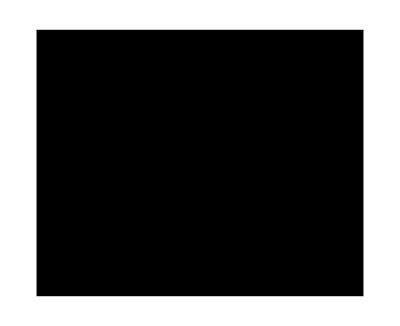

```mathematica
rectangle = Graphics[BoundingRegion[new]]
```

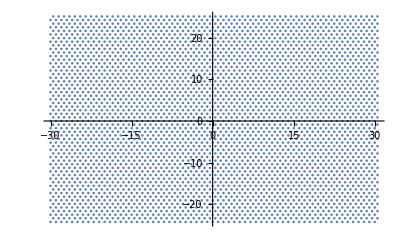

```mathematica
ListPlot[new]
```

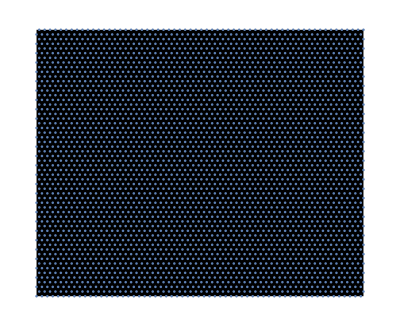

```mathematica
Show[rectangle, %]
```